# Examen 2: Temas de física 4

Ariadna Uxue Palomino Ylla 20161343

```mathematica
Clear["Global`*"];
```

```mathematica
attractor[{f_,g_,h_},{x0_,y0_,z0_},tf_]:=ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/.NDSolve[{x'[t]==f[x[t],y[t],z[t]],y'[t]==g[x[t],y[t],z[t]],z'[t]==h[x[t],y[t],z[t]],x[0]==x0,y[0]==y0,z[0]==z0},{x[t],y[t],z[t]},{t,0,tf},MaxSteps->Infinity]],{t,0,tf},PlotPoints->40000,PlotStyle->{RGBColor[0.84,0.75,0.16],Directive[AbsoluteThickness[1.1]]}](*plot del atractor*)
```

```mathematica
plot[p1_,p2_]:=Show[{p1,p2},PlotRange->All,BoxStyle->Directive[Dashed],AxesLabel->{"x","y","z"},AxesEdge->Automatic,Ticks->Automatic,PlotRange->All,ImageSize->{1000,1000},PlotLabel->HoldForm[Atractor],LabelStyle->{FontFamily->"Clear Sans Light",13,GrayLevel[0]}](*muestra los plots*)
```

```mathematica
InitialCondition[{x0_,y0_,z0_},r_]:=Quiet@Graphics3D[{RGBColor[0.5,0.23,0.5],Specularity[White,5],Sphere[{x0,y0,z0},r]}](*plota una esfera donde inicia el atractor*)
```

```mathematica
plano[orient_,posici_,t_:7]:=If[orient=="XY",XY[t,posici],If[orient=="YZ",YZ[t,posici],XZ[t,posici]]];(*para ver la posición de la sección de Poincar*)
```

```mathematica
XY[t_,posici_]:=Graphics3D[{EdgeForm[None],Opacity[.7],Hue[RandomReal[]],Polygon[{{-t,-t,posici},{t,-t,posici},{t,t,posici},{-t,t,posici}}]}];
```

```mathematica
YZ[t_,posici_]:=Graphics3D[{EdgeForm[None],Opacity[.7],Hue[RandomReal[]],Polygon[{{posici,-t,-t},{posici,-t,t},{posici,t,t},{posici,t,-t}}]}];
```

```mathematica
XZ[t_,posici_]:=Graphics3D[{EdgeForm[None],Opacity[.7],Hue[RandomReal[]],Polygon[{{-t,posici,-t},{-t,posici,t},{t,posici,t},{t,posici,-t}}]}];
```

```mathematica
Poincare[{f_,g_,h_},{x0_,y0_,z0_},tf_,l_:5]:=ListPlot[Reap[NDSolve[{{x'[t]==f[x[t],y[t],z[t]],y'[t]==g[x[t],y[t],z[t]],z'[t]==h[x[t],y[t],z[t]]},x[0]==x0,y[0]==y0,z[0]==z0,WhenEvent[Chop[x[t],10^-5]+0*y[t]+0*z[t]==0.(*Guarda los eventos(y,z) donde x==0 (o mas cercano que ±10^-5)*),Sow[{y[t],z[t]}]]},{},{t,0,tf},MaxSteps->∞,MaxStepSize->.00005]][[-1,1]],ImageSize->{1000,1000},PlotRange->{{-l,l},{-l,l}},PlotRangeClipping->True,AspectRatio->Automatic,Frame->True,PlotStyle->{Purple,PointSize[0.0045]},AxesLabel->{"y[t]","z[t]"},PlotLabel->HoldForm[Sección de Poincare]];  (*Plot de la sección de poincare mediante los puntos (y,z) cuya coordenada x es 0 en algun momento de la trayectoria*)
```

```mathematica
sensibx[{f_,g_,h_},{x0_,y0_,z0_},δ_,tf_]:=Show[{Plot[Evaluate[x[t]/.NDSolve[{x'[t]==f[x[t],y[t],z[t]],y'[t]==g[x[t],y[t],z[t]],z'[t]==h[x[t],y[t],z[t]],x[0]==x0,y[0]==y0,z[0]==z0},{x,y,z},{t,0,tf},MaxSteps->∞]],{t,0,tf},PlotStyle->RGBColor[0.5,0.79,0.5]],Plot[Evaluate[x[t]/.NDSolve[{x'[t]==f[x[t],y[t],z[t]],y'[t]==g[x[t],y[t],z[t]],z'[t]==h[x[t],y[t],z[t]],x[0]==x0+δ,y[0]==y0+δ,z[0]==z0+δ},{x,y,z},{t,0,tf},MaxSteps->∞]],{t,0,tf},PlotStyle->RGBColor[0.5,0.2,0.5]]},ImageSize->Full,AxesLabel->{HoldForm[t],HoldForm[x[t]]},
PlotLabel->HoldForm[Sensibilidad a las condiciones iniciales x[t]],LabelStyle->{FontFamily->"Clear Sans Light",13,GrayLevel[0]}]
```

```mathematica
sensiby[{f_,g_,h_},{x0_,y0_,z0_},δ_,tf_]:=Show[{Plot[Evaluate[y[t]/.NDSolve[{x'[t]==f[x[t],y[t],z[t]],y'[t]==g[x[t],y[t],z[t]],z'[t]==h[x[t],y[t],z[t]],x[0]==x0,y[0]==y0,z[0]==z0},{x,y,z},{t,0,tf},MaxSteps->∞]],{t,0,tf},PlotStyle->RGBColor[0.5,0.79,0.5]],Plot[Evaluate[y[t]/.NDSolve[{x'[t]==f[x[t],y[t],z[t]],y'[t]==g[x[t],y[t],z[t]],z'[t]==h[x[t],y[t],z[t]],x[0]==x0+δ,y[0]==y0+δ,z[0]==z0+δ},{x,y,z},{t,0,tf},MaxSteps->∞]],{t,0,tf},PlotStyle->RGBColor[0.5,0.2,0.5]]},ImageSize->Full,AxesLabel->{HoldForm[t],HoldForm[y[t]]},
PlotLabel->HoldForm[Sensibilidad a las condiciones iniciales y[t]],LabelStyle->{FontFamily->"Clear Sans Light",13,GrayLevel[0]}]
```

```mathematica
sensibz[{f_,g_,h_},{x0_,y0_,z0_},δ_,tf_]:=Show[{Plot[Evaluate[z[t]/.NDSolve[{x'[t]==f[x[t],y[t],z[t]],y'[t]==g[x[t],y[t],z[t]],z'[t]==h[x[t],y[t],z[t]],x[0]==x0,y[0]==y0,z[0]==z0},{x,y,z},{t,0,tf},MaxSteps->∞]],{t,0,tf},PlotStyle->RGBColor[0.5,0.79,0.5]],Plot[Evaluate[z[t]/.NDSolve[{x'[t]==f[x[t],y[t],z[t]],y'[t]==g[x[t],y[t],z[t]],z'[t]==h[x[t],y[t],z[t]],x[0]==x0+δ,y[0]==y0+δ,z[0]==z0+δ},{x,y,z},{t,0,tf},MaxSteps->∞]],{t,0,tf},PlotStyle->RGBColor[0.5,0.2,0.5]]},ImageSize->Full,AxesLabel->{HoldForm[t],HoldForm[z[t]]},
PlotLabel->HoldForm[Sensibilidad a las condiciones iniciales z[t]],LabelStyle->{FontFamily->"Clear Sans Light",13,GrayLevel[0]}]
```

```mathematica
Sensib[S_,CI_,δ_,tf_,eje_]:=If[eje=="x",sensibx[S,CI,δ,tf],If[eje=="y",sensiby[S,CI,δ,tf],sensibz[S,CI,δ,tf]]](*diferencia de una coordenada en el tiempo segun dos condiciones inciales*)
```

```mathematica
DataPS[{f_,g_,h_},{x0_,y0_,z0_},tf_,step_]:=Flatten[Table[Evaluate[x[t]/.NDSolve[{x'[t]==f[x[t],y[t],z[t]],y'[t]==g[x[t],y[t],z[t]],z'[t]==h[x[t],y[t],z[t]],x[0]==x0,y[0]==y0,z[0]==z0},{x,y,z},{t,0,tf},MaxSteps->1000000]],{t,0,tf,step}],1];(*extrae data x(t)*)
```

```mathematica
PS[data_,h_]:=ListPlot[Abs[Chop[Take[Fourier[data],-(Length[data]-1)]]],PlotRange->{{0,Length[data]/2},{0,h}},Joined->True,PlotStyle->RGBColor[0.21,0.52,0.57],AxesLabel->{"K","S"},ImageSize->{1000,422},AspectRatio->Full,PlotLabel->HoldForm[Espectro de poder],LabelStyle->{FontFamily->"Clear Sans Light",13,GrayLevel[0]}](*plot del espectro de poder UTILIZANDO LA FFT y filtrando un poco la data*)
```

```mathematica
PPS[data_,l_]:=ListPlot[Transpose[{Drop[data,-1],Drop[data,1]}],PlotStyle->{Hue[0.7]},AspectRatio->1,BaseStyle->{FontSize->14},ImageSize->{1000,1000},PlotRange->{{-l,l},{-l,l}},PlotRangeClipping->True,AspectRatio->Automatic,Frame->True,AxesLabel->{"X_n","X_(n + 1)"},PlotLabel->HoldForm[Pseudo espacio],LabelStyle->{FontFamily->"Clear Sans Light",14,GrayLevel[0]}](*plot del pseudoespacio centrado en (0,0)*)
```

```mathematica
PPS2[data_,l_]:=ListPlot[Transpose[{Drop[data,-1],Drop[data,1]}],PlotStyle->{Hue[0.7]},AspectRatio->1,BaseStyle->{FontSize->14},ImageSize->{1000,1000},PlotRange->Automatic,PlotRangeClipping->True,AspectRatio->Automatic,Frame->True,AxesLabel->{"X_n","X_(n + 1)"},PlotLabel->HoldForm[Pseudo espacio],LabelStyle->{FontFamily->"Clear Sans Light",14,GrayLevel[0]}](*plot del pseudoespacio no centrado*)
```

```mathematica
DataPlot[data_]:=ListPlot[data,PlotRange->All,Joined->True,PlotStyle->Hue[2],ImageSize->Full,AxesLabel->{HoldForm[t],HoldForm[X[t]]},PlotLabel->None,LabelStyle->{GrayLevel[0]}];(*para ver la data*)
```

## Pregunta 2

## a) Dado el sistema:

```mathematica
f1[x_,y_,z_]=y;
```

```mathematica
g1[x_,y_,z_]=-x+y*z;
```

```mathematica
h1[x_,y_,z_]=a-y^2;
```

```mathematica
S1={f1,g1,h1};(*Guardando el sistema en un array*)
```

```mathematica
CI={0.,5.,0.};(*Guardando las condiciones iniciales en un array*)
```

```mathematica
a=1;    (* Parámetros *)
```

Graficando el atractor para determinar si presenta conducta caótica:

```mathematica
I0=InitialCondition[CI,0.1];(*Graficando el punto de inicio*)
```

```mathematica
A1=attractor[S1,CI,2000];(*Graficando el atractor tf=2000*)
```

```mathematica
plot[A1,I0]
```

-Graphics3D-

```mathematica
Manipulate[Module[{sol},
With[{a=aa,x0=xx0,y0=yy0,z0=zz0},sol=Quiet@NDSolve[{x'[t]==y[t],y'[t]==-x[t]+ y[t]*z[t],z'[t]==a-y[t]^2,x[0]==x0,y[0]==y0,z[0]==z0},{x[t],y[t],z[t]},{t,0,tt},MaxSteps->Infinity];ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/.sol],{t,0,sol[[1,1,2,0,1,1,2]]},PlotPoints->40000,Axes->True,AxesLabel->{"x","y","z"},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},Boxed->False,ImageSize->{900,900},PlotRange->All,PlotStyle->{RGBColor[0.57,0.18,0.88],Directive[AbsoluteThickness[1.1]]}]]],{{tt,2000,"t"},0,2000,.4,ImageSize->Small,Appearance->"Labeled"},
Delimiter,
Style["Parámetros",Bold],
{{aa,1,"a"},0.1,10,.1,ImageSize->Small,Appearance->"Labeled"},Delimiter,Style["Condiciones Iniciales",Bold],
{{xx0,0,"x_0"},0,100,.1,ImageSize->Small,Appearance->"Labeled"},{{yy0,5,"y_0"},1,100,.1,ImageSize->Small,Appearance->"Labeled"},{{zz0,0,"z_0"},0,100,.1,ImageSize->Small,Appearance->"Labeled"},ControlPlacement->Left]
```

Graficando el plano de corte seccional donde se obtendra la sección de Poincaré:

```mathematica
P1=plano["YZ",0,5];(*plano en YZ*)
```

```mathematica
plot[A1,P1]
```

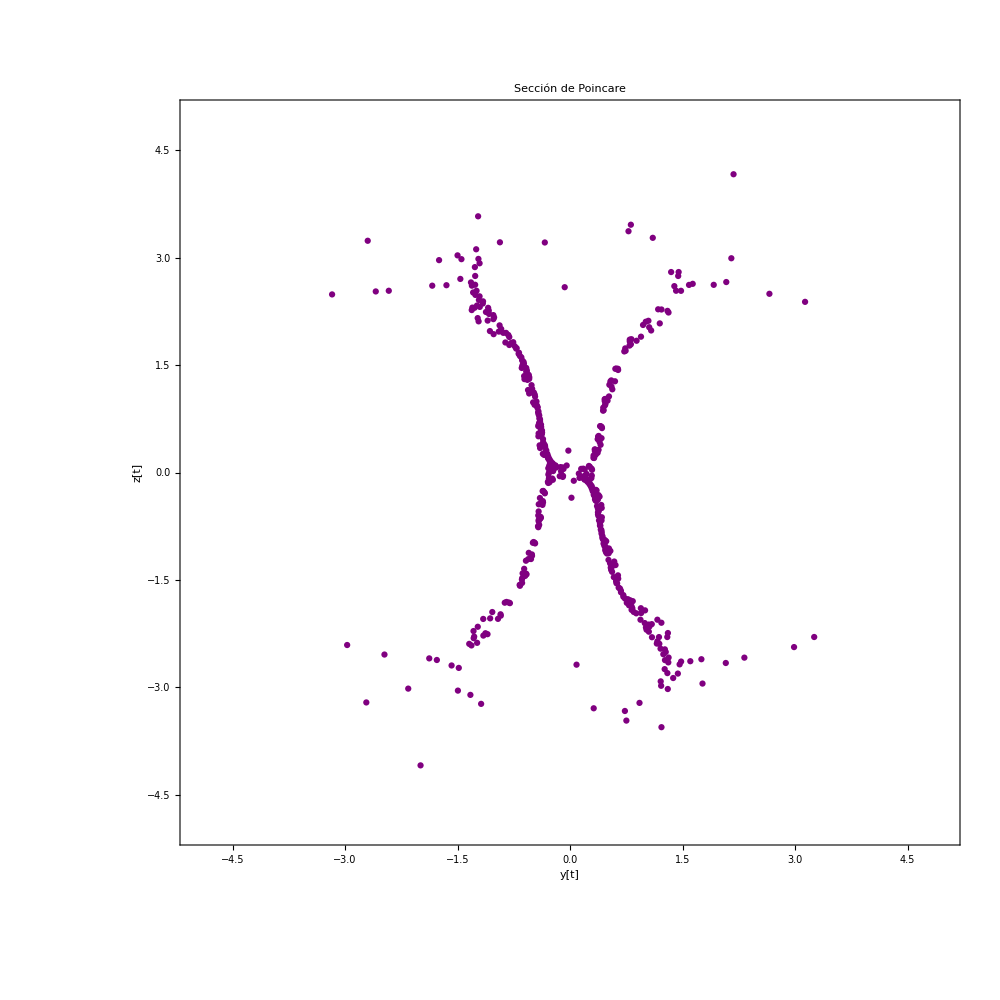

```mathematica
Poincare[S1,CI,2000](*Sección de Poincare tf=2000*)
```

Observamos que la forma que presenta el sistema en la sección no es de naturaleza periodica ni cuasiperiodica ni aleatoria, sino de naturaleza caótica pues presenta una forma singular. La dinámica del sistema se muestra caótica.

Como este algortimo depende del tamaño del paso puede diferir un poco del resultado optimo, reduciendo el tamaño de los pasos o utilizando un Chop con más rango se pueden mejorar los resultados a coste de mayor tiempo de evaluación. Otro modo de obtener el mismo plot:

```mathematica
ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/.NDSolve[{x'[t]==f1[x[t],y[t],z[t]],y'[t]==g1[x[t],y[t],z[t]],z'[t]==h1[x[t],y[t],z[t]],x[0]==0,y[0]==5,z[0]==0},{x[t],y[t],z[t]},{t,0,2000},MaxSteps->Infinity]],{t,0,2000},PlotPoints->40000,PlotStyle->{RGBColor[0.84,0.75,0.16],Directive[AbsoluteThickness[4]]},PlotRange->{{0,0.02},{-5,5},{-5,5}},ViewPoint->{Infinity,0,0},ImageSize->{1000,1000},Axes->{False,True,True},Ticks->{None,Automatic,Automatic}]
```

-Graphics3D-

Graficando la componente x vs el tiempo para ver (en una dimensión) si hay sensibilidad a las condiciones iniciales:

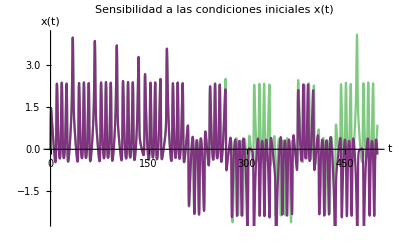

```mathematica
Sensib[S1,CI,0.001,500,"x"](*Aumentando en 0.001 unidades cada una de las coordenadas iniciales tf=500*)
```

Podemos observar como al inicio se encuentran ambas trayectorias muy cercanas pero se comienzan a alejar a pesar de que la diferencia de sus condiciones iniciales es pequeña.  Observamos una alta sensibilidad a las condiciones inciales.

Tambien podemos ver como influye el cambio en las condiciones inciales en las otras dimenciones:

```mathematica
Y1=Sensib[S1,CI,0.001,500,"y"];
```

```mathematica
Z1=Sensib[S1,CI,0.001,500,"z"];
```

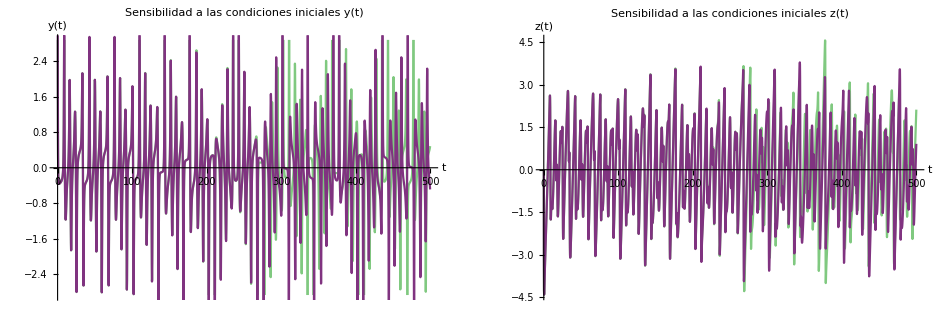

```mathematica
GraphicsRow[{Y1,Z1}]
```

Extrayendo un conjunto de datos del sistema:

```mathematica
D1=DataPS[S1,CI,500,0.4];(*Sistema 1, condiciones 1, tf=500, paso=0.4 EJE X*)
```

Estableciendo el espectro de poder (a partir de data del eje x) mediante la transformada discreta de Fourier:

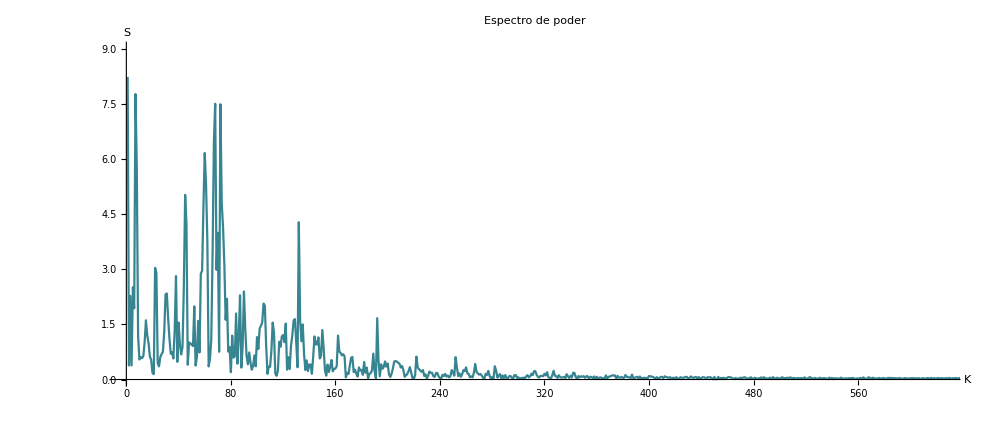

```mathematica
PS[D1,9]
```

Observamos un espectro continuo, característico de una señal caótica.

Por todo lo anterior, se concluye que exhibe naturaleza caótica.

## b) Analizar mediante la sensibilidad a las condiciones iniciales, espectro de poder y pseudoespacio, si el siguiente sistema presenta una dinamica caótica:

```mathematica
f2[x_,y_,z_]=-α*x-4*y-4*z-y^2;
```

```mathematica
g2[x_,y_,z_]=-α*y-4*z-4*x-z^2;
```

```mathematica
h2[x_,y_,z_]=-α*z-4*x-4*y-x^2;
```

```mathematica
S2={f2,g2,h2};(*Guardando el sistema en un array*)
```

```mathematica
CI2={-5.,0.,0.};(*Guardando las condiciones iniciales en un array*)
```

```mathematica
α=1.27;    (* Parámetros *)
```

Graficando el atractor para determinar si presenta conducta caótica:

```mathematica
I1=InitialCondition[CI2,0.18];(*Graficando el punto de inicio*)
```

```mathematica
A2=attractor[S2,CI2,300];(*Graficando el atractor tf=300*)
```

```mathematica
plot[A2,I1]
```

-Graphics3D-

```mathematica
Manipulate[Module[{sol},
With[{α=aa,x0=xx0,y0=yy0,z0=zz0},sol=Quiet@NDSolve[{x'[t]==-α*x[t]-4*y[t]-4*z[t]-y[t]^2,y'[t]==-α*y[t]-4*z[t]-4*x[t]-z[t]^2,z'[t]==-α*z[t]-4*x[t]-4*y[t]-x[t]^2,x[0]==x0,y[0]==y0,z[0]==z0},{x[t],y[t],z[t]},{t,0,tt},MaxSteps->Infinity];ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/.sol],{t,0,sol[[1,1,2,0,1,1,2]]},PlotPoints->40000,Axes->True,AxesLabel->{"x","y","z"},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},Boxed->False,ImageSize->{900,900},PlotRange->All,PlotStyle->{RGBColor[0.57,0.18,0.88],Directive[AbsoluteThickness[1.1]]}]]],{{tt,300,"t"},0,300,.4,ImageSize->Small,Appearance->"Labeled"},
Delimiter,
Style["Parámetros",Bold],
{{aa,1.27,"α"},0.27,10.27,.1,ImageSize->Small,Appearance->"Labeled"},Delimiter,Style["Condiciones Iniciales",Bold],
{{xx0,-5,"x_0"},-5,100,.1,ImageSize->Small,Appearance->"Labeled"},{{yy0,0,"y_0"},0,100,.1,ImageSize->Small,Appearance->"Labeled"},{{zz0,0,"z_0"},0,100,.1,ImageSize->Small,Appearance->"Labeled"},ControlPlacement->Left]
```

Graficando la componente x vs el tiempo para ver (en una dimensión) si hay sensibilidad a las condiciones iniciales:

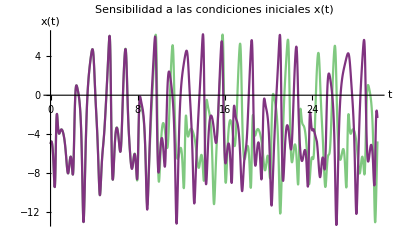

```mathematica
sensibx[S2,CI2,0.0001,30](*Aumentando en 0.0001 unidades cada una de las coordenadas iniciales tf=30*)
```

Podemos observar como al inicio se encuentran ambas trayectorias muy cercanas pero se comienzan a alejar a pesar de que la diferencia de sus condiciones iniciales es pequeña. Observamos una alta sensibilidad a las condiciones inciales.

Tambien podemos ver como influye el cambio en las condiciones inciales en las otras dimenciones:

```mathematica
Y2=Sensib[S2,CI2,0.0001,30,"y"];
```

```mathematica
Z2=Sensib[S2,CI2,0.0001,30,"z"];
```

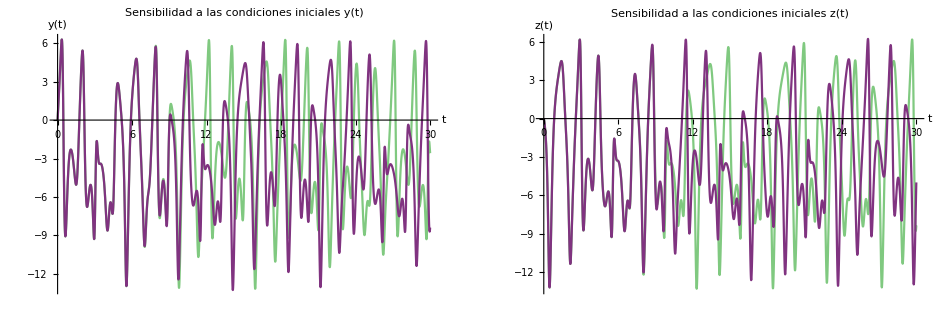

```mathematica
GraphicsRow[{Y2,Z2}]
```

Extrayendo un conjunto de datos del sistema:

```mathematica
D2=DataPS[S2,CI2,500,0.1];(*Sistema 2, condiciones 2, tf=500, paso=0.1*)
```

Estableciendo el pseudo espacio de fase:

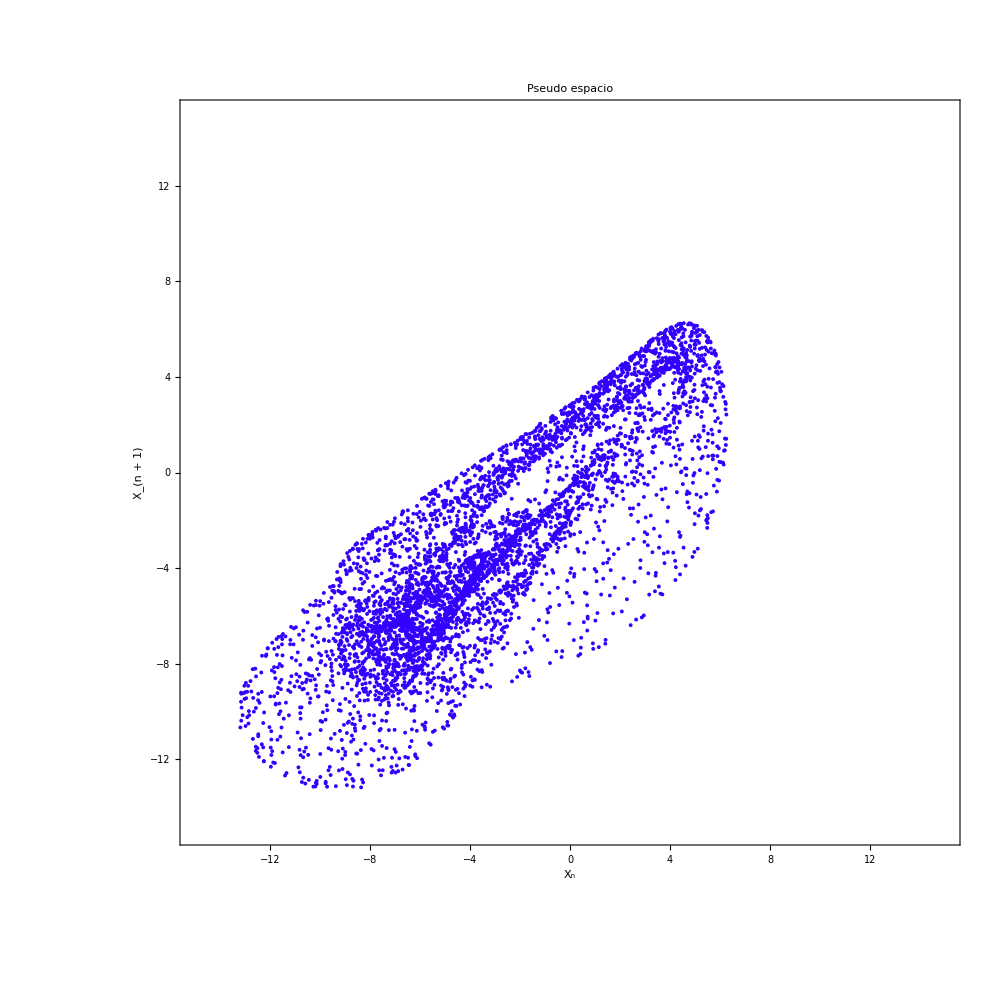

```mathematica
PPS[D2,15]
```

Podemos observar que el patrón del conjunto de datos obtenido parece evidenciar cierta relación entre los valores x_n y x_(n+1), por lo cual el sistema presenta una naturaleza caótica determinista. Ampliando la imagen:

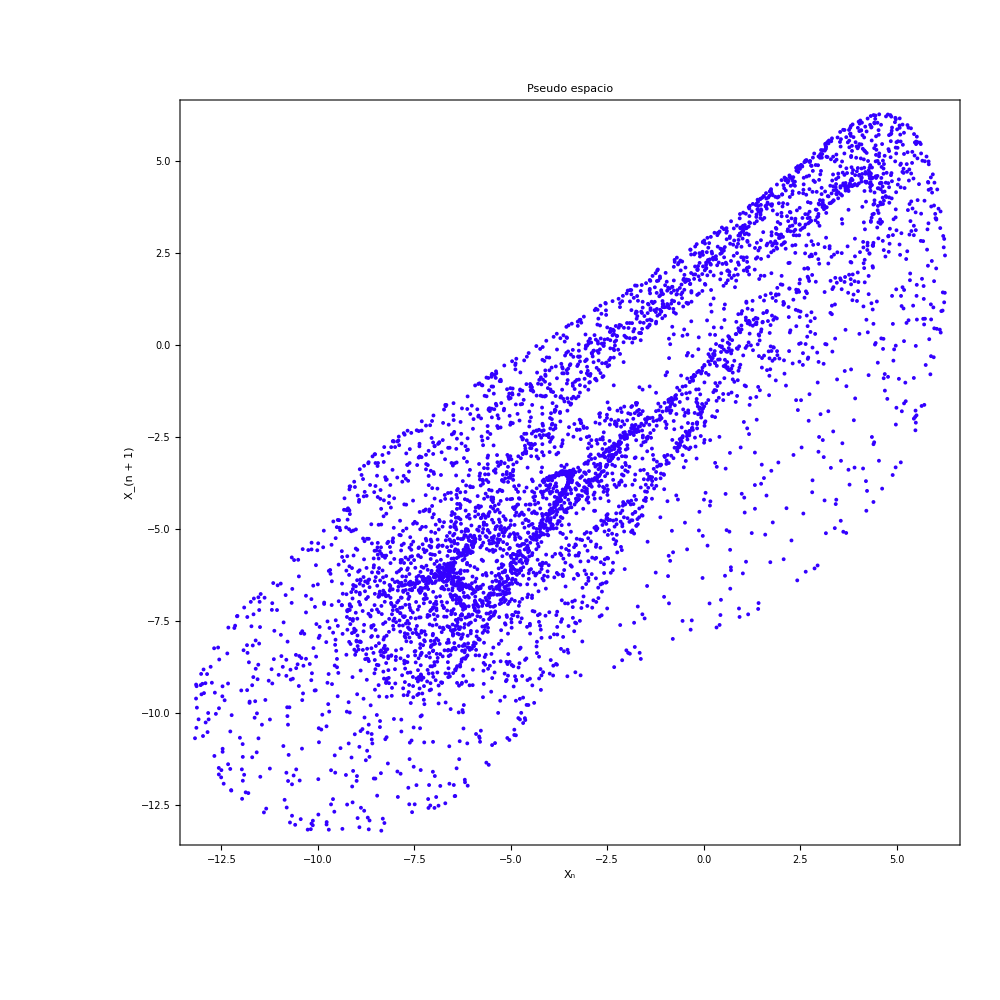

```mathematica
PPS2[D2,15]
```

Extrayendo un conjunto de datos del sistema:

```mathematica
D3=DataPS[S2,CI2,100,0.1];(*Sistema 2, condiciones 2, tf=100, paso=0.1 EJE X tf=100*)
```

Estableciendo el espectro de poder mediante la transformada discreta de Fourier:

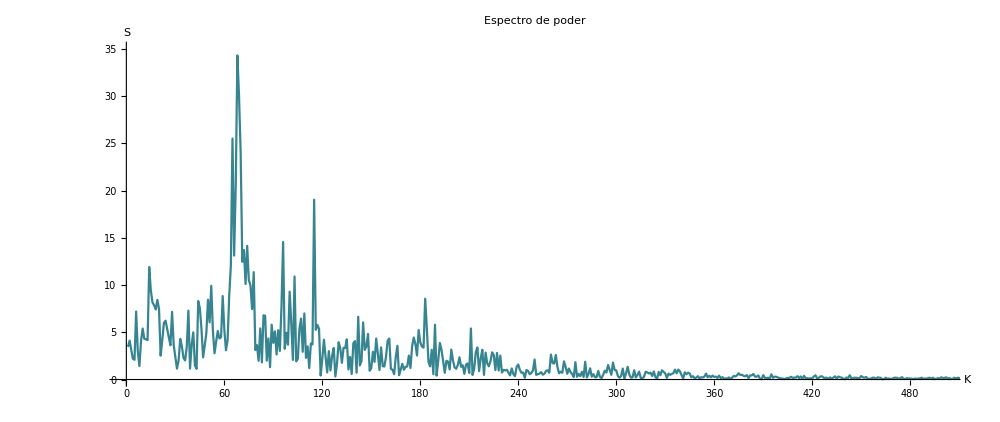

```mathematica
PS[D3,35]
```

Observamos un espectro continuo, característico de una señal caótica.

Por todo lo anterior, se concluye que exhibe naturaleza caótica.

### Anexos:

Plot de los datos en bruto extraidos en a) para el espectro de poder:

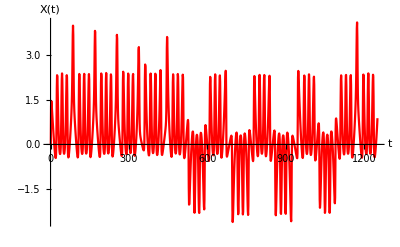

```mathematica
DataPlot[D1]
```

Plot de los datos en bruto extraidos en b) para el pseudoespacio:

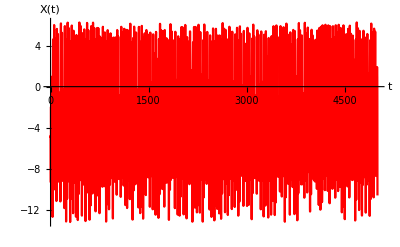

```mathematica
DataPlot[D2]
```

Plot de los datos en bruto extraidos en b) para el espectro de poder:

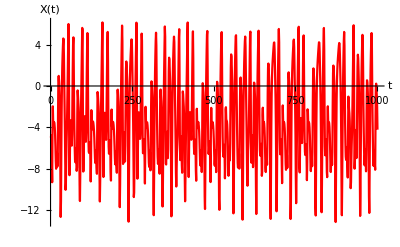

```mathematica
DataPlot[D3]
```